{1,1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3)}

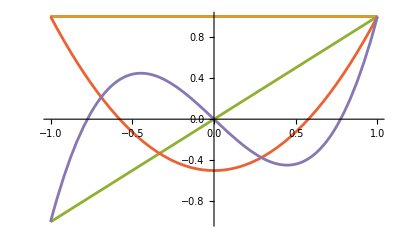

{0,0,1,3 x,1/2 (-3+15 x^2)}

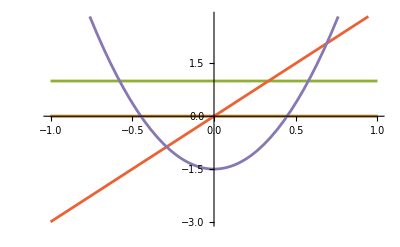

```mathematica
Clear[x];
tmp=LegendreP[#,x]&/@{-1,0,1,2,3}
Plot[tmp,{x,-1,1}]
tmp=D[LegendreP[#,x],x]&/@{-1,0,1,2,3}
Plot[tmp,{x,-1,1}]
```